```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doEPlot=True;
doSteepest=True;
showAll=False;

(** Adaptivity **)
BoostRatio=1.05;
RefineRatio=0.8;
MaxCorrections=50;
ErrorRatio=1.0;

(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.00;

showMistakes=False;
fps=0;

(* Tracker values *)
historyAmt=50;
RefreshInterval=50;
);
InitIterationSettings[];
```

```mathematica
RegenData[]:=(GenData=((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet));
UpdateError[]:=AError=DataN(Total[(GenData-Data)^2]/(DataLength-1))^0.5;
InitFunctionData[paramVariance_,manualTrueParams_, noiseDistribution_,forceData_,arbitfunc_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

If[doNormalize,DataN=Max[Abs@Data];Data/=DataN;,DataN=1];

(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions if there is no arbitrary minimizing function, of course *)
doArbitraryFitting=(arbitfunc=!={});
If[doArbitraryFitting,
eFunc=N@arbitfunc,
oFunc=Mean[(N@#1-N@#2)^2]&;
eFunc=paramh/._[vars__]:>Function[{vars},oFunc[
((Fitfunction@@Prepend[{vars},#])&/@SamplingSet),
Data]
]
];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
factor=factorx;

Corrections=0;
ConsecCorrections=0;

dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;

dir=gFunc@@iterParams;
debugErr={err};
doPerturb=False;
RegenData[];
UpdateError[];
);
LinePlot[points_, size_,amount_]:=Show[ListPointPlot3D[{If[amount>0&&size>amount,points[[-amount;;-1]],points]},PlotRange->All,ImageSize->Medium],Graphics3D@Line@If[amount>0&&size>amount,points[[-amount;;-1]],points]];
Default[RefreshSPlot,1]="Speed";
RefreshSPlot[goal_.]:=Module[{dims=Take[#,2]&/@debugParams},
If[varamt≠2,Return[False]];
SPlot=Evaluate@ContourPlot[
eFunc@@{x,y,0},
Evaluate@({x,-1.+Min@#,1.+Max@#}&@(First/@dims)),
Evaluate@({y,-1.+Min@#,1.+Max@#}&@(Last/@dims)),
PlotLegends->Automatic,PerformanceGoal->goal,ImageSize->300,PlotRange->All];];
SLinePlot[points_,size_,amount_]:=Show[SPlot,Graphics@Line@(If[amount>0&&size>amount,points[[-amount;;-1]],points])];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{If[doArbitraryFitting,"Arbitrary Optimization",
ListPlot[{DataN*GenData,DataN*Data},
Joined->True,ImageSize->Medium,PlotLegends->None]],

If[doPoint,Which[
varamt==3,LinePlot[debugParams,totalIter,historyAmt],
varamt==2,SLinePlot[debugParams,totalIter,historyAmt],
True,"Incorrect dimensionality"],"Disabled"],

If[doEPlot,ListLogLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]},

{"Parameters, dir, Delta",
"Iterations, corrections, α, β, LSTolerance, factor",
"Deviation, Objective"},

{If[showAll||varamt<5,Column[{iterParams,dir,cdir}],"Displaying parameters would take too much space."],
Column[{{totalIter,Corrections},{ProgressIndicator[ConsecCorrections/MaxCorrections],α,β},{LSTol,factor}}],
{AError,debugErr[[-1]]}}

},Frame->All,ItemSize->30];
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];

(*Golden Ratio Search*)
Default[GoldenRatioSearch,8]=False;(* Enforce positivity *)
Default[GoldenRatioSearch,9]=False; (* Verbose *)
Default[GoldenRatioSearch,10]=0; (* Constrain iterations *)
GoldenRatioSearch[coeff_,init_,d_,surface_,tolerance_,min_,LSTemp_,pos_.,verbose_.,max_.]:=Module[{
gr=N@GoldenRatio,f=coeff,l=coeff-LSTemp,h=coeff+N@GoldenRatio*LSTemp,g=coeff+N@GoldenRatio*LSTemp-LSTemp,
e=surface@@(init+#*d)&,i=0,eg,ef,eh,el,
goLeft,goRight,trials=If[verbose,{}]},
While[Abs[f-g]>tolerance&&(max==0||(max≠0&&i++<max)),
If[verbose,trials=Append[trials,{l,f,g,h}]];
eg=e@g;ef=e@f;eh=e@h;el=e@l;
If[eh<ef&&eh<eg,h+=(h-l)*gr;,(* Imbalanced *)
If[el<ef&&el<eg,If[pos,If[And@@Positive@{h-gr h,l-gr*(h-l)},l=Max[h-gr h,l-gr (h-l)],l=0;h=f;];,l=l-gr (h-l)],(* Ensure l is always positive *)
If[ef<eg,h=g,l=f](* No Problems *)];];
f=h-(h-l)/gr;g=l+(h-l)/gr;
];
If[verbose,trials=Append[trials,{l,f,g,h}];Return@trials,Return@f];
];

BackLineSearch[coeff_,init_,d_,surface_,tolerance_,min_,boost_,refine_]:=Module[
{a=coeff*boost,
e=surface@@(init+#*d)&},
While[e@a>min,
a*=refine];
Return@a
];

Clamp[v_,max_]:=If[Norm@v>max,Return@(v*cdir/(cdir.cdir)^0.5),Return@v];

ConjFormula[curr_,prev_]:=curr.(N@(curr-prev))/N@(prev.prev);

RefineFactor[f_]:=(f*=RefineRatio^AccelRefine;ConsecCorrections++;Corrections++;AccelRefine+=AccelAmt;AccelBoost=1.;Return@f);
BoostFactor[f_,ceil_]:=(ConsecCorrections=0;f*=BoostRatio^AccelBoost;AccelRefine=1.;If[f>ceil,Return@ceil]AccelBoost+=AccelAmt;Return@f);
PolyN[degree_]:=Total@(Array[Slot,degree+1,2]*Flatten@MapIndexed[#1^(#2-1)&,Slot/@ConstantArray[1,degree+1]]);
Iterate[n_,tolerance_,min_,factor_,maxn_,temp_,prate_,pmax_]:=Module[{i=0,ω=factor,heat=temp},(
If[totalIter==0,
(* First Iteration *)
dir=-gFunc@@iterParams;
err=eFunc@@iterParams;
(* Start off on the right foot: Beware too large norm *)
If[Norm@dir>1,ω=0;{heat,LSTol}/=dir.dir;
Print["Warning: Large first norm! ",Norm@dir," ",ω," ",LSTol]
];
InternalGRS=GoldenRatioSearch[ω,iterParams,dir,eFunc,LSTol,err,heat,True,True,300];
α=(Last@InternalGRS)[[2]];
iterParams+=α*dir;
cdir=prevdir=dir;
];
ω=factor;
heat=temp;
(* Successive Iteration *)
While[(i<n &&(NoErr||(AError>tolerance&&Norm@dir>min))),
If[doPoint&&varamt==2&&Mod[totalIter,RefreshInterval]==0,RefreshSPlot["Speed"];];
If[doPerturb&&Norm@cdir<prate,iterParams+=Min[pmax,ω]*Normalize[RandomReal[1.,varamt]]];
dir=-gFunc@@iterParams;
err=eFunc@@iterParams;
β=Max[0,ConjFormula[dir,prevdir]];
cdir=dir+β*cdir;
α=GoldenRatioSearch[ω,iterParams,cdir,eFunc,LSTol,err,heat];
iterParams+=α*cdir;
If[eFunc@@iterParams>err,
ConsecCorrections++;
Corrections++;
iterParams-=α cdir;
heat*=0.5;ω*=0.667;
,
ConsecCorrections=0;
ω=Min[factor,1.5 ω];heat=Min[temp,2.0 heat];
AddToHistory[];
prevdir=dir;i++;
If[fps≠0,Pause[fps];];
totalIter++;
RegenData[];
UpdateError[];
];
]
)];

HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@DataLength-1)/DataLength],FourierParameters->{0,2/DataLength}];
FindMax[list_]:=Position[list,Max@list][[1,1]];
FindIndexFreq[index_]:=N@((#-2+2(FindMax@HDFD@#-1)/DataLength)*2π*SamplingRate/DataLength)&/@index;
RecoverIndices[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
RecoverFreqList[]:=(Select[RecoverIndices[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=2;
DataLength=50;
SamplingRate=50;
StdDev=0.24;
doNormalize=True;
Fitfunction=#2Exp[#3#1]&;
InitFunctionData[5.,{},NormalDistribution[0,StdDev],{},{}];
```

```mathematica
(* BEGIN ITERATION *)
Smoothness=1;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;

RefreshInterval=100;
InitIterationSettings[];
showMistakes=True;
doSteepest=True;

showAll=True;
historyAmt=0;
LSTemp=0.005;
LSTol=0.001;

InitIterationData[0.01,{}];
RefreshSPlot["Speed"];
doPerturb=False;
Column[{
Visualize[],
ToSpacedString@{"Frequency indices: ", RecoverIndices[]},
ToSpacedString@{"Data frequencies: ", RecoverFreqList[]},
ToSpacedString@{If[doNormalize,"","Not "],"Normalized"},
If[showAll||varamt<5,
Column[{ToSpacedString@{"TrueParams",TrueParams},ToSpacedString@{"InitialParams",iterParams},ToSpacedString@{"FitFunction:",InputForm@Fitfunction}}],
"Displaying parameters would take too much space."
],
ToSpacedString@{"LSTemp and LSTolerance:",LSTemp,LSTol},
ToSpacedString@{"Original Standard Deviation:",StdDev}
}]
```

Frequency indices:  {1, 10, 13, 17, 22, 24}
Data frequencies:  {1.25664, 54.0354, 74.8956, 100.28, 130.439, 143.257}
 Normalized
TrueParams {-1.53985, -3.95417}
InitialParams {3.18814, -3.59962}
FitFunction: #2*Exp[#3*#1] & 
LSTemp and LSTolerance: 0.005 0.001
Original Standard Deviation: 0.24

```mathematica
(*** Iteration loop ***)
NoErr=False;
ITol=0.01/DataN;
IMin=10.^-9/DataN;
MaxNorm=50;
Iterate[15,ITol,IMin,0.05,MaxNorm,LSTemp,0.1,2.]//AbsoluteTiming
RefreshSPlot["Quality"];
```

Warning: Large first norm! 1.149 0 0.000757465

{1.04842,Null}

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{RecordedComparisonData,
{{{"Smoothness",Smoothness},
debugErr,debugParams,TotalRefines,
{"Balance",Balance},{"Impatience",Impatience},{"Iterations",totalIter}}}}];
```

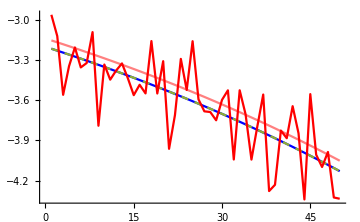

-Graphics3D-

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
GenData,
(Fitfunction@@Prepend[TrueParams,#])&/@SamplingSet,
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},
Joined->True,ImageSize->Medium,PlotStyle->{Blue,Pink,Dashed,Red}]
LinePlot[debugParams,Length@debugParams,Length@debugParams]
```

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[
Join[
Flatten@ToSpacedString/@RecordedComparisonData[[sm,{1,7,5,6}]],
{ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]},
ToSpacedString@{"Corrections:",RecordedComparisonData[[sm,4]]}}
]
],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel",
LegendLayout->"Row"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
PlotRange->All,
ImageSize->1200,
Joined->True,
PlotMarkers->{Automatic,4}]
```

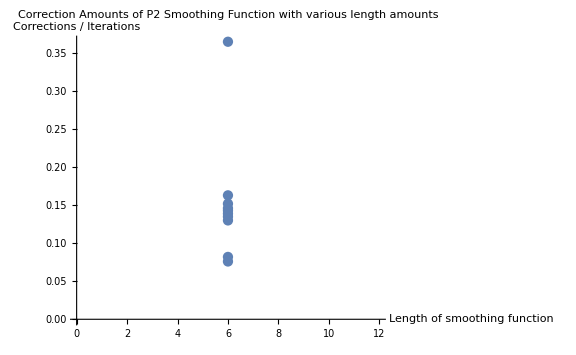

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,2]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```

0.0561803
0.00809997
0.00809997
@
{5.34195,3.21859}
@@
{5.34195,3.21859}

0.0589801

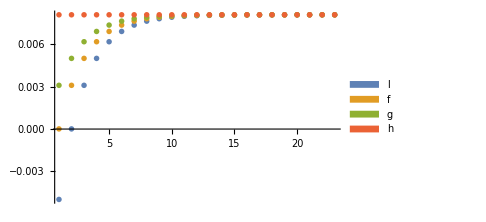
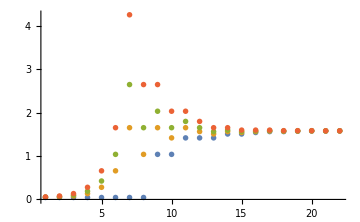

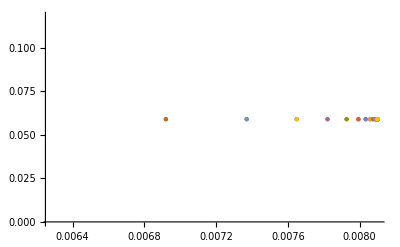

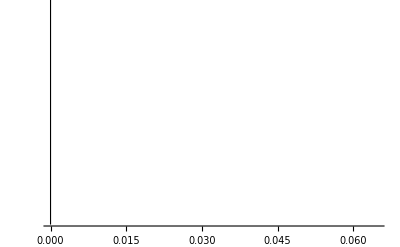

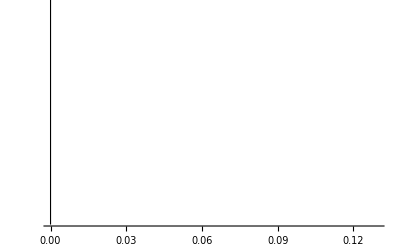

```mathematica
GRSts=eFunc;
GRSit=iterParams;
GRSd=cdir;
GRSg=dir;
GRSi=0.00001;
GRStol=0.0000001;
GRSpos=True;
gscale=8;

GRSR=GoldenRatioSearch[GRSi,GRSit,GRSd,GRSts,GRStol,err,LSTemp,GRSpos,True,100];
GRSD=GoldenRatioSearch[GRSi,GRSit,GRSg,GRSts,GRStol,err,LSTemp,GRSpos,True,100];

Column@{α,γ=(Last@GRSR)[[2]],τ=(Last@GRSD)[[2]],"@",iterParams+τ dir,"@@",iterParams+α dir}
err
Row[{ListPlot[Transpose@GRSR,PlotLegends->SwatchLegend[{l,f,g,h}],ImageSize->Medium,PlotRange->All],ListPlot[Transpose@InternalGRS,PlotRange->All,ImageSize->Medium]},Frame->True]
EFC=eFunc@@(iterParams+#*cdir)&;
EFG=eFunc@@(iterParams+#*(gFunc@@iterParams))&;
(*Manipulate[Show[
ListPlot[Map[{#,EFC@#}&,GRSR,{2}]⟦i;;i+k⟧,PlotStyle->{PointSize@Small,PointSize@Large}],
Plot[err,{i,-10,10}]
],{i,1,Length@GRSR-k,1},{k,1,Length@GRSR-1,1},ContinuousAction->False]*)
ListPlot[Map[{#,EFC@#}&,GRSR,{2}],PlotStyle->{PointSize@Small,PointSize@Large}]
Show[Plot[{EFC@x,err},{x, 0,gscale γ}],Graphics@Point@{γ,EFC@γ}]
Show[Plot[{EFG@x,err},{x, 0,gscale 2τ}],Graphics@Point@{τ,EFG@τ}]
```

```mathematica
If[showAll||varamt<5,Column[{iterParams,dir,cdir}],"Displaying parameters would take too much space."];
```

```mathematica
StandardDeviation@(GenData-Data)
DataN*%
```

0.0604319

0.216767